# Markov Matrix

## is a matrix related the X[n] state to X[n + 1] state

```mathematica
Clear[R,P,F]
```

```mathematica
MatrixLog[A_]:=Module[{P,G,v,LD},
{v,G}=Eigensystem[A];
P=Transpose[G];
LD=Table[If[i==j,Chop[Log[v[[i]]]],0],{i,1,Length[A]},{j,1,Length[A]}];
P.LD.Inverse[P]
]
```

```mathematica
M={
{0.1,0.4,0.1},
{0.1,0.4,0.8},
{0.8,0.2,0.1}};
M//MatrixForm
Table[Sum[M[[i,j]],{i,1,Length[M]}],{j,1,Length[M]}]
Mp=Limit[MatrixPower[M,n],n->∞]//Chop;
Mp//MatrixForm
Eigensystem[M]
```

(0.1 | 0.4 | 0.1
0.1 | 0.4 | 0.8
0.8 | 0.2 | 0.1)

{1.,1.,1.}

(0.236025 | 0.236025 | 0.236025
0.453416 | 0.453416 | 0.453416
0.310559 | 0.310559 | 0.310559)

{{1.,-0.2+0.412311 ⅈ,-0.2-0.412311 ⅈ},{{-0.394615,-0.758076,-0.51923},{0.188982+0.389597 ⅈ,-0.661438+0. ⅈ,0.472456-0.389597 ⅈ},{0.188982-0.389597 ⅈ,-0.661438+0. ⅈ,0.472456+0.389597 ⅈ}}}

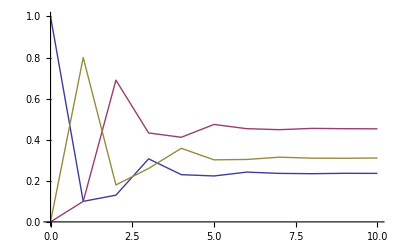

```mathematica
Xm=Table[{n,(MatrixPower[M,n].UnitVector[Length[M],1])[[i]]},{i,1,Length[M]},{n,0,10}];
g1=ListPlot[Xm,Joined->True]
```

## Relation with Rate matrix

```mathematica
Rm=M-IdentityMatrix[Length[M]];
Rm//MatrixForm
Flatten[NullSpace[Rm]]/(Flatten[NullSpace[Rm]].Table[1,{i,1,Length[Rm]}])
```

(-0.9 | 0.4 | 0.1
0.1 | -0.6 | 0.8
0.8 | 0.2 | -0.9)

{0.236025,0.453416,0.310559}

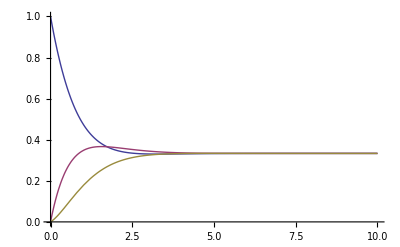

```mathematica
g2=Plot[Evaluate[MatrixExp[Rm t].UnitVector[Length[Rm],1]],{t,0,10},PlotRange->All]
```

```mathematica
Rml=MatrixLog[M]//Chop;
Rml//MatrixForm
Eigensystem[Rml]//Chop
Table[Sum[Rml[[i,j]],{i,1,Length[Rml]}]//Chop,{j,1,Length[Rml]}]
 Flatten[NullSpace[Rml]]/(Flatten[NullSpace[Rml]].Table[1,{i,1,Length[Rml]}])
```

(-0.513888 | 0.756947 | -0.714587
-1.82455 | -0.152314 | 1.60903
2.33843 | -0.604633 | -0.894446)

{{-0.780324+2.02243 ⅈ,-0.780324-2.02243 ⅈ,0},{{0.188982+0.389597 ⅈ,-0.661438,0.472456-0.389597 ⅈ},{0.188982-0.389597 ⅈ,-0.661438,0.472456+0.389597 ⅈ},{0.394615,0.758076,0.51923}}}

{0,0,0}

{0.236025,0.453416,0.310559}

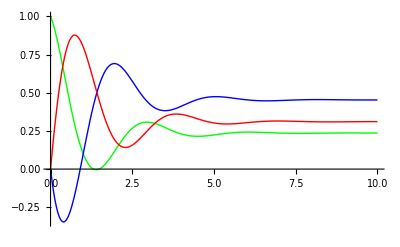

```mathematica
g3=Plot[Evaluate[Re[MatrixExp[Rml t].UnitVector[Length[Rml],1]]],{t,0,10},PlotRange->All,PlotStyle->Table[Hue[i/Length[Rml]],{i,1,Length[Rml]}]]
```

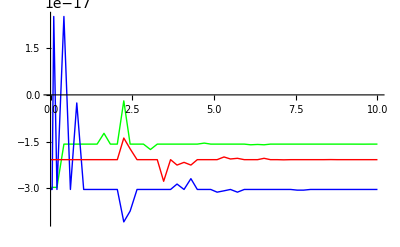

```mathematica
g4=Plot[Evaluate[Im[MatrixExp[Rml t].UnitVector[Length[Rml],1]]],{t,0,10},PlotRange->All,PlotStyle->Table[Hue[i/Length[Rml]],{i,1,Length[Rml]}]]
```

## Compare

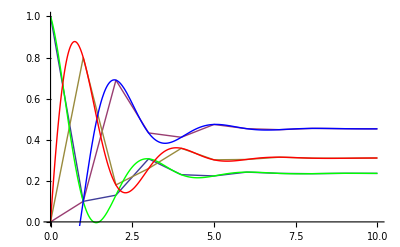

```mathematica
Show[g1,g3]
```